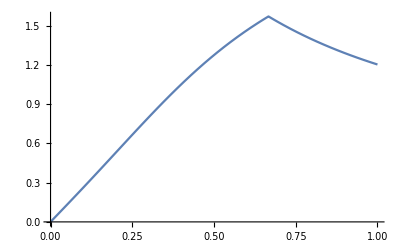

```mathematica
Plot[ArcTan[1/(√(4/(27 x^2)-1+x))],{x,0,1}]
```

NDSolve::ndsz: At x == 6.66138, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {-19.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-0.01345570.6666

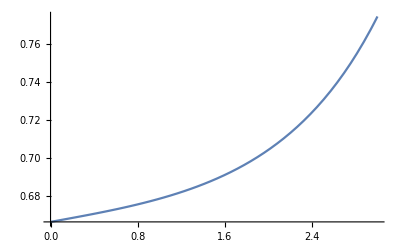

```mathematica
Clear[y];
u0=N[(0.9999(43-1))/(num-1)];
α=ArcTan[1/(√(4/(27 u0^2)-1+u0))];
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==-u0 Cot[1.01α(64)/num]},y,{x,0,18}];
t=y/.sol[[1,1]];
root=x/.FindRoot[t[x],{x,1}][[1]];
Print[root,u0];
Plot[t[x],{x,0,3}]
```

```mathematica
root
```

0.549003

```mathematica
num=64;
points=Table[Table[0,{j,1,num}],{i,1,num}];
root=0.04;
For[i=2,i<num+1,i++,
Clear[y];
u0=N[(0.9999(i-1))/(num-1)];
α=ArcTan[1/(√(4/(27 u0^2)-1+u0))];
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==-u0 Cot[1.01α]},y,{x,0,18}];
t=y/.sol[[1,1]];
If[i==44,root=11.8];
root=x/.FindRoot[t[x],{x,root}][[1]];
points[[i,num]]=root;
root1=root;
For[j=num-1,j>1,j--,
Clear[y];
sol=NDSolve[{y''[x]+y[x]-3/2 y[x]^2==0,y[0]==u0,y'[0]==-u0 Cot[1.01α(j-1)/num]},y,{x,0,18}];
t=y/.sol[[1,1]];
root1=x/.FindRoot[t[x],{x,root1 j/(j+1)}][[1]];
points[[i,j]]=root1;
];
]
```

NDSolve::ndsz: At x == 10.5093, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 9.92009, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At x == 9.52903, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-3.48653} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-9.79458} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-20.5241} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

```mathematica
Export["E:\\files\\C++\\BlackHole\\BlackHoleRendering\\BlackHoleRendering\\BlackHoleRendering\\resources\\case1_.txt",points,"Table"]
```

E:\files\C++\BlackHole\BlackHoleRendering\BlackHoleRendering\BlackHoleRendering\resources\case1_.txt

```mathematica
points
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.000643829,0.00128766,0.00193149,0.00257532,0.00321915,0.00386298,0.00450681,0.00515064,0.00579447,0.0064383,0.00708213,0.00772596,0.00836979,0.00901362,0.00965745,0.0103013,0.0109451,0.0115889,0.0122328,0.0128766,0.0135204,0.0141643,0.0148081,0.0154519,0.0160958,0.0167396,0.0173834,0.0180273,0.0186711,0.0193149,0.0199588,0.0206026,0.0212464,0.0218903,0.0225341,0.0231779,0.0238218,0.0244656,0.0251094,0.0257533,0.0263971,0.0270409,0.0276848,0.0283286,0.0289725,0.0296163,0.0302601,0.030904,0.0315478,0.0321917,0.0328355,0.0334793,0.0341232,0.034767,0.0354109,0.0360547,0.0366986,0.0373424,0.0379863,0.0386301,0.0392739,0.0399178,0.0412055},{0,0.00128864,0.00257727,0.00386591,0.00515454,0.00644318,0.00773182,0.00902046,0.0103091,0.0115977,0.0128864,0.014175,0.0154637,0.0167523,0.018041,0.0193296,0.0206183,0.0219069,0.0231956,0.0244842,0.0257729,0.0270616,0.0283502,0.0296389,0.0309276,0.0322163,0.033505,0.0347936,0.0360823,0.037371,0.0386597,0.0399484,0.0412372,0.0425259,0.0438146,0.0451033,0.046392,0.0476808,0.0489695,0.0502583,0.051547,0.0528358,0.0541246,0.0554133,0.0567021,0.0579909,0.0592797,0.0605685,0.0618573,0.0631461,0.0644349,0.0657238,0.0670126,0.0683014,0.0695903,0.0708792,0.072168,0.0734569,0.0747458,0.0760347,0.0773236,0.0786125,0.0799014,0.0824793},{0,0.00193522,0.00387044,0.00580565,0.00774088,0.0096761,0.0116113,0.0135466,0.0154818,0.017417,0.0193523,0.0212876,0.0232228,0.0251581,0.0270934,0.0290287,0.030964,0.0328993,0.0348347,0.03677,0.0387054,0.0406408,0.0425761,0.0445116,0.046447,0.0483824,0.0503179,0.0522534,0.0541889,0.0561244,0.05806,0.0599956,0.0619312,0.0638668,0.0658025,0.0677381,0.0696738,0.0716096,0.0735453,0.0754811,0.0774169,0.0793528,0.0812887,0.0832246,0.0851606,0.0870965,0.0890326,0.0909686,0.0929047,0.0948408,0.096777,0.0987132,0.100649,0.102586,0.104522,0.106458,0.108395,0.110331,0.112268,0.114204,0.116141,0.118078,0.120014,0.123888},{0,0.00258419,0.00516838,0.00775258,0.0103368,0.012921,0.0155052,0.0180895,0.0206737,0.023258,0.0258423,0.0284266,0.031011,0.0335954,0.0361798,0.0387642,0.0413487,0.0439332,0.0465178,0.0491024,0.0516871,0.0542718,0.0568565,0.0594414,0.0620262,0.0646112,0.0671961,0.0697812,0.0723663,0.0749515,0.0775368,0.0801221,0.0827075,0.085293,0.0878786,0.0904642,0.09305,0.0956358,0.0982217,0.100808,0.103394,0.10598,0.108566,0.111153,0.113739,0.116326,0.118913,0.121499,0.124086,0.126674,0.129261,0.131848,0.134435,0.137023,0.139611,0.142199,0.144787,0.147375,0.149963,0.152551,0.15514,0.157729,0.160317,0.165495},{0,0.00323599,0.00647199,0.009708,0.012944,0.0161801,0.0194162,0.0226523,0.0258885,0.0291247,0.0323609,0.0355973,0.0388336,0.0420701,0.0453067,0.0485433,0.05178,0.0550168,0.0582537,0.0614908,0.0647279,0.0679652,0.0712026,0.0744401,0.0776777,0.0809155,0.0841535,0.0873916,0.0906299,0.0938683,0.097107,0.100346,0.103585,0.106824,0.110063,0.113303,0.116543,0.119783,0.123023,0.126263,0.129504,0.132745,0.135986,0.139228,0.142469,0.145711,0.148954,0.152196,0.155439,0.158682,0.161925,0.165169,0.168413,0.171657,0.174902,0.178147,0.181392,0.184638,0.187883,0.19113,0.194376,0.197623,0.200871,0.207367},{0,0.0038909,0.0077818,0.0116727,0.0155637,0.0194547,0.0233458,0.027237,0.0311282,0.0350196,0.038911,0.0428026,0.0466944,0.0505862,0.0544783,0.0583705,0.0622629,0.0661555,0.0700483,0.0739414,0.0778347,0.0817282,0.085622,0.0895161,0.0934105,0.0973052,0.1012,0.105095,0.108991,0.112887,0.116784,0.12068,0.124577,0.128475,0.132373,0.136271,0.14017,0.144069,0.147969,0.151869,0.15577,0.159671,0.163573,0.167475,0.171378,0.175281,0.179185,0.18309,0.186995,0.1909,0.194807,0.198713,0.202621,0.206529,0.210438,0.214347,0.218258,0.222168,0.22608,0.229992,0.233905,0.237819,0.241734,0.249565},{0,0.004549,0.00909802,0.0136471,0.0181962,0.0227455,0.0272948,0.0318443,0.036394,0.0409438,0.0454939,0.0500442,0.0545947,0.0591456,0.0636967,0.0682482,0.0728,0.0773522,0.0819048,0.0864578,0.0910113,0.0955652,0.10012,0.104675,0.10923,0.113786,0.118343,0.1229,0.127458,0.132016,0.136576,0.141136,0.145696,0.150258,0.15482,0.159383,0.163946,0.168511,0.173076,0.177643,0.18221,0.186778,0.191347,0.195918,0.200489,0.205061,0.209634,0.214208,0.218784,0.22336,0.227938,0.232516,0.237096,0.241677,0.24626,0.250843,0.255428,0.260014,0.264602,0.269191,0.273781,0.278372,0.282965,0.292156},{0,0.00521025,0.0104205,0.0156309,0.0208414,0.0260521,0.0312629,0.036474,0.0416854,0.0468971,0.0521092,0.0573217,0.0625346,0.067748,0.0729619,0.0781764,0.0833915,0.0886072,0.0938237,0.0990408,0.104259,0.109477,0.114697,0.119918,0.125139,0.130361,0.135585,0.140809,0.146034,0.151261,0.156489,0.161718,0.166948,0.17218,0.177412,0.182647,0.187882,0.193119,0.198358,0.203598,0.208839,0.214082,0.219327,0.224574,0.229822,0.235072,0.240324,0.245577,0.250833,0.25609,0.261349,0.26661,0.271874,0.277139,0.282407,0.287676,0.292948,0.298222,0.303498,0.308776,0.314057,0.31934,0.324626,0.335204},{0,0.00587444,0.011749,0.0176236,0.0234984,0.0293735,0.0352489,0.0411247,0.047001,0.0528778,0.0587552,0.0646332,0.0705119,0.0763915,0.0822718,0.0881531,0.0940354,0.0999187,0.105803,0.111689,0.117575,0.123464,0.129353,0.135244,0.141136,0.14703,0.152926,0.158823,0.164722,0.170623,0.176525,0.18243,0.188337,0.194245,0.200156,0.206069,0.211984,0.217902,0.223822,0.229744,0.235669,0.241597,0.247527,0.25346,0.259395,0.265334,0.271275,0.277219,0.283166,0.289117,0.29507,0.301027,0.306987,0.31295,0.318916,0.324886,0.33086,0.336836,0.342817,0.348801,0.354789,0.360781,0.366777,0.37878},{0,0.00654121,0.0130825,0.019624,0.0261658,0.0327081,0.0392508,0.0457941,0.0523381,0.0588829,0.0654286,0.0719753,0.0785231,0.0850721,0.0916224,0.0981741,0.104727,0.111282,0.117839,0.124397,0.130957,0.137519,0.144083,0.15065,0.157219,0.16379,0.170363,0.176939,0.183518,0.1901,0.196684,0.203272,0.209863,0.216456,0.223053,0.229654,0.236257,0.242865,0.249476,0.256091,0.262709,0.269332,0.275958,0.282589,0.289224,0.295863,0.302507,0.309155,0.315808,0.322465,0.329127,0.335794,0.342467,0.349144,0.355826,0.362513,0.369206,0.375905,0.382609,0.389318,0.396033,0.402754,0.409481,0.422952},{0,0.00721006,0.0144203,0.0216308,0.0288417,0.0360533,0.0432655,0.0504787,0.0576929,0.0649082,0.0721249,0.0793431,0.0865629,0.0937844,0.101008,0.108233,0.115461,0.122691,0.129924,0.137159,0.144397,0.151638,0.158882,0.166129,0.17338,0.180634,0.187891,0.195153,0.202419,0.209688,0.216962,0.22424,0.231523,0.23881,0.246103,0.2534,0.260702,0.26801,0.275322,0.282641,0.289965,0.297295,0.30463,0.311972,0.31932,0.326675,0.334036,0.341403,0.348778,0.356159,0.363547,0.370942,0.378345,0.385755,0.393173,0.400599,0.408032,0.415473,0.422923,0.43038,0.437847,0.445321,0.452804,0.467797},{0,0.00788037,0.015761,0.023642,0.0315236,0.0394061,0.0472896,0.0551743,0.0630606,0.0709485,0.0788383,0.0867302,0.0946244,0.102521,0.110421,0.118323,0.126228,0.134137,0.14205,0.149966,0.157886,0.16581,0.173739,0.181672,0.18961,0.197554,0.205502,0.213456,0.221415,0.22938,0.237351,0.245329,0.253313,0.261303,0.269301,0.277305,0.285317,0.293336,0.301363,0.309398,0.31744,0.325491,0.333551,0.341619,0.349696,0.357782,0.365877,0.373982,0.382096,0.39022,0.398354,0.406499,0.414654,0.422819,0.430995,0.439183,0.447381,0.455591,0.463812,0.472045,0.48029,0.488547,0.496817,0.513393},{0,0.00855139,0.0171031,0.0256553,0.0342085,0.0427628,0.0513185,0.059876,0.0684355,0.0769974,0.0855618,0.0941292,0.1027,0.111274,0.119852,0.128433,0.13702,0.14561,0.154206,0.162807,0.171414,0.180026,0.188644,0.197269,0.2059,0.214538,0.223184,0.231837,0.240498,0.249166,0.257844,0.26653,0.275224,0.283928,0.292642,0.301365,0.310098,0.318842,0.327596,0.336361,0.345137,0.353925,0.362724,0.371536,0.38036,0.389196,0.398045,0.406907,0.415782,0.424672,0.433575,0.442492,0.451423,0.46037,0.469331,0.478307,0.487299,0.496307,0.505331,0.514371,0.523428,0.532501,0.541591,0.559824},{0,0.00922228,0.018445,0.0276684,0.036893,0.0461192,0.0553474,0.0645779,0.0738112,0.0830476,0.0922875,0.101531,0.110779,0.120032,0.12929,0.138554,0.147823,0.157099,0.166381,0.17567,0.184967,0.194271,0.203584,0.212905,0.222236,0.231575,0.240925,0.250284,0.259654,0.269035,0.278428,0.287832,0.297248,0.306676,0.316118,0.325572,0.33504,0.344523,0.354019,0.36353,0.373057,0.382598,0.392156,0.40173,0.411321,0.420928,0.430553,0.440195,0.449856,0.459535,0.469233,0.47895,0.488687,0.498443,0.50822,0.518018,0.527836,0.537676,0.547537,0.557421,0.567327,0.577255,0.587207,0.607181},{0,0.0098921,0.0197847,0.0296784,0.0395736,0.0494709,0.0593708,0.0692737,0.0791804,0.0890911,0.0990065,0.108927,0.118853,0.128786,0.138725,0.148672,0.158626,0.168589,0.17856,0.188541,0.198531,0.208532,0.218544,0.228567,0.238602,0.248649,0.25871,0.268784,0.278871,0.288973,0.299091,0.309223,0.319372,0.329537,0.339719,0.349919,0.360136,0.370372,0.380628,0.390902,0.401197,0.411513,0.421849,0.432207,0.442587,0.452989,0.463415,0.473864,0.484336,0.494834,0.505356,0.515904,0.526478,0.537079,0.547706,0.55836,0.569043,0.579754,0.590493,0.601262,0.612061,0.62289,0.633749,0.655562},{0,0.0105599,0.0211204,0.0316822,0.0422461,0.0528127,0.0633827,0.0739566,0.0845353,0.0951194,0.10571,0.116306,0.126911,0.137523,0.148144,0.158774,0.169415,0.180066,0.190729,0.201404,0.212092,0.222793,0.233508,0.244238,0.254983,0.265745,0.276523,0.287319,0.298133,0.308966,0.319818,0.330691,0.341584,0.352498,0.363435,0.374395,0.385378,0.396385,0.407417,0.418474,0.429558,0.440668,0.451806,0.462972,0.474166,0.48539,0.496644,0.507928,0.519244,0.530592,0.541972,0.553386,0.564833,0.576315,0.587833,0.599386,0.610975,0.622601,0.634265,0.645967,0.657708,0.669489,0.68131,0.705073},{0,0.955689,0.0224498,0.0336769,0.0449065,0.0561396,0.0673769,0.0786194,0.0898679,0.101123,0.112386,0.123658,0.134939,0.146231,0.157533,0.168848,0.180176,0.191517,0.202873,0.214244,0.225632,0.237037,0.248459,0.259901,0.271363,0.282845,0.294349,0.305875,0.317424,0.328997,0.340595,0.352219,0.36387,0.375548,0.387255,0.39899,0.410756,0.422553,0.434381,0.446242,0.458137,0.470066,0.48203,0.49403,0.506067,0.518142,0.530255,0.542408,0.554601,0.566835,0.579111,0.59143,0.603792,0.616198,0.62865,0.641148,0.653693,0.666285,0.678926,0.691616,0.704357,0.717148,0.72999,0.755833},{0,0.956353,0.0237709,0.035659,0.0475504,0.0594461,0.0713472,0.0832548,0.0951699,0.107094,0.119027,0.130971,0.142928,0.154897,0.16688,0.178878,0.190893,0.202924,0.214975,0.227044,0.239134,0.251246,0.263381,0.275539,0.287723,0.299932,0.312168,0.324433,0.336727,0.349051,0.361407,0.373795,0.386217,0.398673,0.411166,0.423695,0.436262,0.448869,0.461515,0.474203,0.486933,0.499707,0.512525,0.525389,0.5383,0.551258,0.564265,0.577323,0.590431,0.603591,0.616805,0.630073,0.643396,0.656776,0.670213,0.683708,0.697263,0.710879,0.724556,0.738296,0.7521,0.765968,0.779903,0.807972},{0,0.956886,1.19534,0.0376254,0.0501735,0.0627269,0.075287,0.0878552,0.100433,0.113021,0.125621,0.138235,0.150863,0.163508,0.17617,0.18885,0.201551,0.214274,0.227019,0.239788,0.252583,0.265405,0.278255,0.291134,0.304045,0.316988,0.329965,0.342977,0.356025,0.369111,0.382236,0.395402,0.40861,0.421861,0.435156,0.448498,0.461887,0.475325,0.488814,0.502354,0.515946,0.529594,0.543296,0.557057,0.570875,0.584753,0.598693,0.612695,0.626762,0.640893,0.655092,0.669358,0.683694,0.698101,0.71258,0.727132,0.74176,0.756463,0.771244,0.786104,0.801045,0.816066,0.831171,0.861633},{0,0.957281,1.19634,1.36052,0.0527715,0.0659767,0.07919,0.0924133,0.105648,0.118896,0.132158,0.145437,0.158734,0.172051,0.185389,0.198751,0.212136,0.225549,0.238989,0.252459,0.26596,0.279495,0.293064,0.306669,0.320313,0.333996,0.347721,0.361489,0.375301,0.389161,0.403068,0.417026,0.431035,0.445098,0.459216,0.47339,0.487624,0.501917,0.516273,0.530692,0.545177,0.559729,0.57435,0.589042,0.603807,0.618645,0.63356,0.648552,0.663624,0.678776,0.694012,0.709332,0.724739,0.740234,0.755819,0.771495,0.787264,0.803128,0.81909,0.835149,0.851308,0.867569,0.883934,0.91698},{0,0.957533,1.19716,1.36194,1.49106,1.59866,0.0830501,0.0969219,0.110808,0.124709,0.138629,0.152568,0.166529,0.180514,0.194526,0.208565,0.222634,0.236735,0.25087,0.265041,0.27925,0.293499,0.30779,0.322126,0.336508,0.350938,0.365419,0.379952,0.39454,0.409185,0.423889,0.438653,0.453481,0.468374,0.483334,0.498363,0.513465,0.528639,0.54389,0.559219,0.574628,0.59012,0.605696,0.621359,0.637111,0.652954,0.66889,0.684922,0.701052,0.717281,0.733613,0.750049,0.766591,0.783242,0.800004,0.816878,0.833869,0.850976,0.868203,0.885551,0.903024,0.920622,0.938348,0.974194},{0,0.957638,1.1978,1.36315,1.49287,1.60109,1.69472,0.101374,0.115904,0.130452,0.145022,0.159616,0.174237,0.188886,0.203566,0.218279,0.233029,0.247817,0.262646,0.277518,0.292436,0.307402,0.322419,0.337489,0.352615,0.367799,0.383044,0.398353,0.413727,0.42917,0.444684,0.460271,0.475935,0.491678,0.507502,0.52341,0.539405,0.555489,0.571665,0.587937,0.604305,0.620774,0.637345,0.654023,0.670808,0.687704,0.704715,0.721841,0.739087,0.756455,0.773947,0.791568,0.809318,0.827201,0.84522,0.863378,0.881677,0.90012,0.91871,0.937449,0.956341,0.975388,0.994592,1.03349},{0,0.957596,1.19825,1.36416,1.49446,1.60328,1.69752,1.78114,0.120929,0.136117,0.151331,0.166573,0.181846,0.197154,0.212498,0.227882,0.243309,0.258782,0.274303,0.289876,0.305503,0.321188,0.336934,0.352743,0.368618,0.384563,0.400581,0.416675,0.432847,0.449101,0.465441,0.481868,0.498387,0.515001,0.531712,0.548524,0.565441,0.582465,0.5996,0.616849,0.634215,0.651702,0.669313,0.687052,0.704922,0.722925,0.741067,0.759349,0.777776,0.796351,0.815077,0.833958,0.852997,0.872199,0.891565,0.9111,0.930808,0.950691,0.970754,0.990999,1.01143,1.03205,1.05287,1.09509},{0,0.957404,1.19851,1.36495,1.49581,1.60521,1.70006,1.78429,1.86041,1.93011,0.157546,0.173428,0.189348,0.205308,0.221311,0.237361,0.253462,0.269617,0.285829,0.302102,0.318439,0.334844,0.351321,0.367873,0.384504,0.401217,0.418017,0.434906,0.451889,0.468968,0.486149,0.503435,0.52083,0.538337,0.55596,0.573704,0.591573,0.609569,0.627698,0.645964,0.664369,0.68292,0.701619,0.720471,0.73948,0.758651,0.777987,0.797492,0.817172,0.83703,0.857071,0.877298,0.897718,0.918333,0.939148,0.960167,0.981396,1.00284,1.0245,1.04638,1.06849,1.09083,1.11341,1.15929},{0,0.957063,1.19859,1.36553,1.49693,1.6069,1.70233,1.78716,1.8639,1.93422,1.99934,2.06014,0.196733,0.213339,0.229995,0.246706,0.263477,0.28031,0.297211,0.314183,0.33123,0.348358,0.365569,0.382868,0.40026,0.417749,0.435339,0.453035,0.470841,0.488761,0.506801,0.524964,0.543256,0.561681,0.580243,0.598949,0.617801,0.636806,0.655968,0.675292,0.694783,0.714446,0.734286,0.754308,0.774518,0.794921,0.815522,0.836325,0.857338,0.878564,0.900009,0.92168,0.94358,0.965717,0.988094,1.01072,1.0336,1.05673,1.08013,1.1038,1.12775,1.15197,1.17648,1.2264},{0,0.956576,1.19849,1.3659,1.49782,1.60834,1.70434,1.78976,1.8671,1.93804,2.00379,2.06524,2.12306,2.17778,0.238541,0.255908,0.273344,0.290852,0.308439,0.326109,0.343867,0.361717,0.379665,0.397717,0.415876,0.434148,0.452538,0.471052,0.489695,0.508472,0.527388,0.54645,0.565662,0.585031,0.604561,0.62426,0.644131,0.664183,0.68442,0.704848,0.725474,0.746303,0.767342,0.788598,0.810076,0.831783,0.853726,0.875911,0.898344,0.921034,0.943985,0.967205,0.990701,1.01448,1.03855,1.06292,1.08759,1.11257,1.13787,1.1635,1.18946,1.21576,1.24241,1.29679},{0,0.955946,1.1982,1.36606,1.49848,1.60953,1.70608,1.79208,1.87001,1.94157,2.00794,2.07002,2.12849,2.18388,2.23661,2.28703,0.283054,0.301234,0.319505,0.337871,0.356339,0.374914,0.393602,0.412409,0.431342,0.450405,0.469606,0.48895,0.508444,0.528094,0.547907,0.567889,0.588046,0.608387,0.628916,0.649642,0.670571,0.691711,0.713068,0.734651,0.756465,0.77852,0.800822,0.82338,0.8462,0.869292,0.892663,0.916321,0.940275,0.964533,0.989103,1.01399,1.03922,1.06477,1.09068,1.11694,1.14357,1.17058,1.19797,1.22575,1.25394,1.28254,1.31157,1.37093},{0,0.955175,1.19774,1.36601,1.49891,1.61048,1.70757,1.79413,1.87264,1.94479,2.01178,2.07449,2.13361,2.18966,2.24306,2.29417,2.34327,2.39059,0.3304,0.349461,0.368639,0.387939,0.407371,0.426939,0.446651,0.466514,0.486536,0.506723,0.527084,0.547625,0.568355,0.58928,0.61041,0.631752,0.653313,0.675104,0.697132,0.719405,0.741932,0.764723,0.787786,0.81113,0.834765,0.858701,0.882946,0.907511,0.932406,0.95764,0.983225,1.00917,1.03549,1.06218,1.08928,1.11677,1.14468,1.17302,1.2018,1.23103,1.26072,1.29089,1.32155,1.35271,1.38439,1.44936},{0,0.95427,1.1971,1.36577,1.49913,1.61118,1.7088,1.79591,1.87499,1.94773,2.01532,2.07866,2.13841,2.19511,2.24919,2.30099,2.35079,2.39884,2.44533,2.49044,2.53433,0.400788,0.420965,0.441299,0.461798,0.48247,0.503324,0.524368,0.545612,0.567063,0.588731,0.610626,0.632756,0.655131,0.677761,0.700657,0.723827,0.747283,0.771034,0.795093,0.819469,0.844174,0.869219,0.894616,0.920377,0.946513,0.973038,0.999964,1.0273,1.05507,1.08327,1.11193,1.14106,1.17067,1.20078,1.2314,1.26254,1.29423,1.32648,1.35931,1.39273,1.42676,1.46142,1.53272},{0,0.953235,1.1963,1.36534,1.49912,1.61166,1.70979,1.79743,1.87707,1.95038,2.01857,2.08252,2.1429,2.20025,2.255,2.30748,2.35799,2.40676,2.454,2.49988,2.54455,2.58815,2.63079,0.455487,0.47678,0.49827,0.519968,0.541884,0.564027,0.586409,0.609039,0.631929,0.655091,0.678534,0.702271,0.726315,0.750676,0.775367,0.800402,0.825793,0.851553,0.877696,0.904236,0.931187,0.958564,0.986382,1.01466,1.0434,1.07264,1.10237,1.13263,1.16343,1.19478,1.22671,1.25924,1.29237,1.32614,1.36057,1.39567,1.43147,1.468,1.50527,1.54332,1.62185},{0,0.952076,1.19534,1.36472,1.49892,1.61191,1.71053,1.79869,1.87887,1.95275,2.02153,2.08608,2.14709,2.20509,2.2605,2.31366,2.36488,2.41438,2.46236,2.50901,2.55448,2.59889,2.64237,2.68502,2.72693,2.76818,0.536468,0.55927,0.582332,0.605665,0.629283,0.653198,0.677423,0.701971,0.726858,0.752096,0.7777,0.803685,0.830067,0.856861,0.884083,0.91175,0.939879,0.968488,0.997594,1.02722,1.05737,1.08808,1.11937,1.15125,1.18375,1.21688,1.25068,1.28517,1.32036,1.3563,1.39299,1.43048,1.46879,1.50795,1.54799,1.58896,1.63088,1.71777},{0,0.9508,1.19422,1.36392,1.49851,1.61194,1.71104,1.7997,1.88042,1.95485,2.0242,2.08935,2.15098,2.20962,2.26569,2.31954,2.37146,2.42168,2.47042,2.51784,2.56411,2.60935,2.65368,2.69722,2.74004,2.78224,2.82389,2.86507,2.90584,0.624837,0.649469,0.674439,0.699763,0.725457,0.751537,0.778021,0.804925,0.832267,0.860066,0.888341,0.917112,0.946398,0.97622,1.0066,1.03756,1.06912,1.10131,1.13415,1.16767,1.20189,1.23684,1.27255,1.30905,1.34636,1.38453,1.42359,1.46357,1.5045,1.54644,1.58943,1.6335,1.67872,1.72514,1.8218},{0,0.949413,1.19296,1.36295,1.49791,1.61177,1.71132,1.80048,1.88171,1.95669,2.02661,2.09235,2.15459,2.21386,2.27059,2.32512,2.37773,2.42869,2.47818,2.52638,2.57346,2.61953,2.66473,2.70916,2.75292,2.79608,2.83874,2.88095,2.9228,2.96434,3.00562,3.04671,0.722126,0.749009,0.776332,0.804116,0.832381,0.86115,0.890443,0.920285,0.950698,0.981707,1.01334,1.04562,1.07857,1.11223,1.14662,1.18178,1.21773,1.25452,1.29217,1.33072,1.37021,1.41068,1.45218,1.49475,1.53844,1.58331,1.6294,1.67678,1.72553,1.7757,1.82739,1.93568},{0,0.947922,1.19157,1.36182,1.49713,1.61139,1.71139,1.80103,1.88277,1.95828,2.02875,2.09507,2.15792,2.21782,2.2752,2.3304,2.38372,2.4354,2.48565,2.53464,2.58253,2.62945,2.67553,2.72087,2.76557,2.80972,2.8534,2.89669,2.93965,2.98234,3.02483,3.06717,3.10943,3.15164,3.19386,0.830409,0.860103,0.890373,0.921246,0.952748,0.984909,1.01776,1.05133,1.08565,1.12076,1.15669,1.19348,1.23116,1.26979,1.3094,1.35003,1.39174,1.43458,1.4786,1.52385,1.57041,1.61834,1.66771,1.7186,1.77111,1.82533,1.88137,1.93935,2.06175},{0,0.946334,1.19005,1.36054,1.49618,1.61083,1.71126,1.80136,1.88359,1.95963,2.03065,2.09754,2.16098,2.2215,2.27953,2.33541,2.38943,2.44184,2.49285,2.54263,2.59134,2.63911,2.68608,2.73235,2.77802,2.82318,2.86791,2.91229,2.95639,3.00028,3.04402,3.08767,3.13129,3.17493,3.21865,3.26249,3.30651,3.35076,0.952528,0.985795,1.01982,1.05464,1.09029,1.12682,1.16426,1.20266,1.24207,1.28253,1.3241,1.36684,1.41079,1.45604,1.50263,1.55066,1.60019,1.65131,1.70413,1.75873,1.81525,1.87381,1.93456,1.99768,2.06335,2.20331},{0,0.944656,1.18841,1.35912,1.49507,1.61009,1.71093,1.80149,1.8842,1.96074,2.0323,2.09976,2.16379,2.22493,2.2836,2.34015,2.39488,2.44802,2.49978,2.55036,2.5999,2.64854,2.69641,2.74362,2.79028,2.83647,2.88227,2.92778,2.97306,3.01819,3.06322,3.10823,3.15328,3.19841,3.2437,3.2892,3.33495,3.38103,3.42747,3.47435,3.5217,1.09245,1.13035,1.16927,1.20924,1.25034,1.29262,1.33615,1.38098,1.4272,1.47488,1.52411,1.57497,1.62756,1.68201,1.73842,1.79694,1.85771,1.92092,1.98676,2.05547,2.12731,2.2026,2.36516},{0,0.942893,1.18666,1.35757,1.49381,1.60918,1.71043,1.80141,1.8846,1.96164,2.03372,2.10174,2.16635,2.2281,2.28742,2.34464,2.40006,2.45394,2.50647,2.55784,2.60822,2.65774,2.70653,2.7547,2.80236,2.8496,2.89651,2.94318,2.98968,3.03608,3.08246,3.12889,3.17542,3.22212,3.26906,3.31629,3.36389,3.4119,3.46039,3.50943,3.55908,3.6094,3.66046,3.71233,1.2559,1.29996,1.34541,1.39233,1.4408,1.49093,1.54281,1.59656,1.6523,1.71017,1.77032,1.83294,1.89822,1.96638,2.0377,2.1125,2.19113,2.27405,2.36181,2.55472},{0,0.941055,1.1848,1.35589,1.49241,1.60812,1.70974,1.80116,1.8848,1.96233,2.03493,2.10349,2.16869,2.23104,2.29099,2.34888,2.40501,2.45961,2.51291,2.5651,2.61632,2.66672,2.71644,2.76559,2.81428,2.8626,2.91065,2.95851,3.00626,3.05399,3.10177,3.14966,3.19775,3.2461,3.29477,3.34384,3.39338,3.44346,3.49414,3.5455,3.59761,3.65056,3.70441,3.75925,3.81518,3.87227,3.93064,3.99038,1.50401,1.55855,1.61521,1.67414,1.73553,1.79955,1.86644,1.93645,2.00988,2.08708,2.16848,2.25458,2.34602,2.44356,2.54821,2.78438},{0,1.89266,1.18285,1.3541,1.49087,1.6069,1.7089,1.80072,1.88481,1.96282,2.03593,2.10504,2.1708,2.23376,2.29434,2.35289,2.40972,2.46506,2.51914,2.57213,2.6242,2.67551,2.72617,2.77632,2.82605,2.87548,2.92469,2.97378,3.02284,3.07194,3.12117,3.1706,3.22032,3.27039,3.32089,3.37191,3.42352,3.47579,3.52882,3.58267,3.63745,3.69324,3.75014,3.80824,3.86766,3.92852,3.99093,4.05503,4.12098,4.18894,4.25909,1.75781,1.8258,1.8971,1.97206,2.05105,2.13453,2.22308,2.31738,2.4183,2.52695,2.64479,2.77378,3.07726},{0,1.88801,2.38896,2.74543,1.48921,1.60555,1.7079,1.80013,1.88465,1.96312,2.03674,2.10637,2.1727,2.23626,2.29747,2.35669,2.41421,2.47029,2.52514,2.57896,2.63189,2.68411,2.73573,2.78689,2.8377,2.88826,2.93867,2.98903,3.03943,3.08996,3.1407,3.19174,3.24316,3.29505,3.34749,3.40057,3.45437,3.509,3.56454,3.62108,3.67875,3.73764,3.79787,3.85956,3.92286,3.9879,4.05485,4.12389,4.19521,4.26904,4.34564,4.42529,4.50834,4.5952,4.68636,2.17963,2.27587,2.37912,2.49059,2.61186,2.74508,2.89323,3.06069,3.48479},{0,1.88324,2.38331,2.73932,3.02684,3.27318,3.49174,3.69018,1.88432,1.96326,2.03736,2.10752,2.17441,2.23856,2.30039,2.36027,2.4185,2.47532,2.53095,2.58559,2.6394,2.69254,2.74514,2.79734,2.84924,2.90096,2.95261,3.00428,3.05607,3.10808,3.16039,3.21311,3.26633,3.32013,3.37461,3.42988,3.48604,3.54318,3.60142,3.66089,3.72169,3.78397,3.84786,3.91353,3.98114,4.05089,4.12297,4.19764,4.27515,4.35581,4.43999,4.5281,4.62066,4.71828,4.82173,4.93197,5.05023,5.17818,5.31802,2.84925,3.02062,3.21936,3.45744,4.16792},{0,1.87837,2.37754,2.73305,3.0203,3.2665,3.48502,3.68351,3.86685,4.03834,4.20037,4.3547,4.50269,4.64544,4.78383,4.91858,5.05031,5.17955,5.30675,5.43234,5.55668,5.68009,5.8029,5.9254,6.04784,6.17051,6.29364,6.4175,6.54233,6.66837,6.79588,6.92511,7.05631,7.18978,3.40234,3.45994,3.51861,3.57846,3.63962,3.70225,3.76648,3.83248,3.90043,3.97052,4.04297,4.11803,4.19597,4.27712,4.36183,4.45055,4.54379,4.64218,4.74649,4.8577,2.3739,2.49738,2.63344,2.78524,2.95743,5.78315,6.02532,6.32887,6.74339,7.50327},{0,1.85468,2.34765,2.69877,2.98245,3.22558,3.44135,3.63731,3.81828,3.98753,4.14739,4.29962,4.44558,4.58632,4.72272,4.85549,4.98525,5.11251,5.23772,5.3613,5.4836,5.60496,5.72566,5.84601,5.96626,6.08667,6.20749,6.32897,6.45134,6.57484,6.69973,6.82623,6.95461,7.08513,7.21806,7.35369,7.49232,7.63428,7.7799,7.92958,8.0837,8.24272,8.40712,8.57744,8.75429,8.93835,9.1304,9.33132,9.54213,9.76405,9.99852,4.60704,4.71141,4.82277,4.94239,2.46874,5.21362,2.75657,2.92899,5.75198,3.36932,3.67187,4.08688,10.232},{0,1.83168,2.31864,2.66549,2.9457,3.18585,3.39894,3.59245,3.77113,3.9382,4.09598,4.24619,4.39017,4.52898,4.66346,4.79434,4.9222,5.04757,5.17088,5.29254,5.4129,5.53228,5.65099,5.7693,5.88746,6.00574,6.12438,6.24361,6.36367,6.48479,6.60721,6.73116,6.8569,6.98468,7.11476,7.24742,7.38296,7.52168,7.66392,7.81005,7.96045,8.11556,8.27583,8.44179,8.61403,8.79318,8.97999,9.1753,9.38008,9.59549,9.82285,4.57144,4.67577,4.78716,4.9069,5.03664,5.17868,5.33618,2.89904,5.71885,5.96335,3.6428,4.05853,10.2064},{0,1.80941,2.29055,2.63326,2.91013,7.14739,3.3579,3.54904,3.7255,3.89047,4.04624,4.19451,4.3366,4.47355,4.60621,4.73526,4.86132,4.98488,5.10638,5.22621,5.34473,5.46224,5.57905,5.69543,5.81163,5.9279,6.04448,6.1616,6.27949,6.39838,6.51849,6.64007,6.76335,6.88858,7.01602,7.14594,7.27863,7.41438,7.55353,7.69643,7.84345,7.99501,8.15157,8.31363,8.48175,8.65656,8.83878,9.02922,9.22882,9.43869,9.6601,9.89463,4.64033,4.7517,4.87149,5.00139,2.54528,5.30158,2.869,3.06937,5.93083,3.61341,6.65838,10.1804},{0,1.78785,2.26335,2.60205,2.87567,3.11014,3.31815,3.507,3.68132,3.84427,3.99811,4.14451,4.28478,4.41994,4.55084,4.67816,4.80248,4.92431,5.04408,5.16217,5.27893,5.39467,5.50969,5.62423,5.73857,5.85294,5.96758,6.08271,6.19856,6.31535,6.43331,6.55266,6.67364,6.7965,6.92148,7.04885,7.1789,7.3119,7.4482,7.58812,7.73204,7.88037,8.03354,8.19207,8.35648,8.5274,8.70553,8.89167,9.08672,9.29177,9.50808,9.73716,4.60513,4.71642,4.83621,4.96621,5.10871,5.26692,5.44556,3.03926,5.89805,3.58376,4.00075,10.1539},{0,1.76696,2.23699,2.57181,2.84229,3.07404,3.27964,3.46627,3.63853,3.79953,3.95149,4.09609,4.23461,4.36806,4.49727,4.62292,4.74558,4.86576,4.98387,5.1003,5.21539,5.32944,5.44274,5.55555,5.66812,5.78069,5.89349,6.00674,6.12066,6.23548,6.3514,6.46866,6.58749,6.70812,6.83081,6.9558,7.08338,7.21383,7.34748,7.48464,7.6257,7.77105,7.92112,8.07641,8.23744,8.40484,8.57927,8.76154,8.95254,9.15333,9.36515,9.5895,9.82818,4.68138,4.80112,4.93115,5.07378,5.23225,5.41128,3.0091,5.86506,6.17465,6.59711,10.1271},{0,1.74672,2.21144,2.54249,2.80992,3.03905,3.2423,3.4268,3.59706,3.75617,3.90633,4.04919,4.18602,4.31782,4.4454,4.56945,4.69052,4.80911,4.92564,5.04048,5.15397,5.26641,5.37808,5.48923,5.60013,5.71099,5.82204,5.93351,6.04561,6.15855,6.27256,6.38785,6.50465,6.62319,6.74371,6.86647,6.99175,7.11981,7.25099,7.38559,7.52399,7.66657,7.81377,7.96607,8.124,8.28815,8.45922,8.63796,8.82529,9.02225,9.23006,9.45022,9.68451,4.64661,4.76624,4.89625,5.03896,5.19763,5.37698,2.97895,5.83192,6.14241,3.94189,10.1},{0,1.72708,2.18667,2.51406,2.77853,3.00512,3.2061,3.38852,3.55685,3.71413,3.86255,4.00373,4.13893,4.26914,4.39516,4.51767,4.63721,4.75428,4.86929,4.98261,5.09456,5.20546,5.31557,5.42515,5.53444,5.64368,5.75307,5.86285,5.97322,6.08439,6.19658,6.31001,6.42489,6.54145,6.65994,6.78061,6.90371,7.02954,7.15839,7.2906,7.42651,7.56651,7.71104,7.86056,8.01561,8.17677,8.34472,8.52024,8.7042,8.89767,9.10185,9.31822,9.54858,9.79514,4.73162,4.86156,5.00429,5.16308,5.3427,5.55048,3.1895,6.10999,3.91219,10.0726},{0,1.70804,2.16263,2.48647,2.74808,2.9722,3.17098,3.35139,3.51785,3.67336,3.8201,3.95966,4.09328,4.22196,4.34647,4.46749,4.58557,4.70117,4.81472,4.92658,5.03707,5.14649,5.25511,5.36318,5.47095,5.57863,5.68645,5.79461,5.90334,6.01283,6.12329,6.23495,6.34801,6.46271,6.57928,6.69796,6.81903,6.94274,7.06941,7.19936,7.33294,7.47052,7.61255,7.75947,7.91183,8.0702,8.23526,8.40778,8.58864,8.77888,8.97973,9.19264,9.41943,9.66229,4.69729,4.8271,4.9698,5.12866,5.30848,5.51662,3.15931,6.07745,3.88235,10.0451},{0,1.68956,2.13929,2.45969,2.71851,2.94024,3.13689,3.31535,3.47999,3.6338,3.7789,3.9169,4.049,4.1762,4.29926,4.41885,4.53551,4.64971,4.76185,4.87231,4.98139,5.08939,5.19659,5.30322,5.40952,5.51572,5.62203,5.72866,5.83582,5.94371,6.05253,6.16251,6.27385,6.38678,6.50152,6.61833,6.73746,6.85918,6.98379,7.11161,7.24298,7.37829,7.51796,7.66245,7.81228,7.96804,8.13039,8.30011,8.47807,8.66532,8.86307,9.07279,9.29629,9.53576,9.79404,4.79292,4.93552,5.0944,5.27436,5.48279,3.12919,6.04482,3.85244,10.0173},{0,1.67161,2.11663,2.43369,2.6898,2.90921,3.10379,3.28035,3.44324,7.59539,3.73892,3.87539,4.00603,4.13179,4.25346,4.37166,4.48696,4.5998,4.7106,4.8197,4.92743,5.03408,5.1399,5.24515,5.35006,5.45484,5.5597,5.66487,5.77053,5.87689,5.98416,6.09253,6.20223,6.31348,6.42649,6.54152,6.65881,6.77864,6.9013,7.0271,7.15639,7.28955,7.42699,7.56918,7.71663,7.86992,8.02973,8.19682,8.37206,8.5565,8.75135,8.9581,9.17853,9.41486,9.66993,4.75903,4.9015,5.06034,5.24037,5.44904,3.09916,6.01215,3.82247,9.98943},{0,1.65418,2.09462,2.40843,2.66191,2.87907,3.07163,3.24636,3.40754,3.55809,3.70008,3.83509,3.96431,4.08869,4.20899,4.32587,4.43984,4.55138,4.66088,4.76868,4.87511,4.98045,5.08496,5.18889,5.29245,5.39587,5.49936,5.60312,5.70735,5.81225,5.91803,6.02488,6.13301,6.24265,6.35402,6.46735,6.58289,6.70093,6.82173,6.94562,7.07294,7.20406,7.33939,7.4794,7.62459,7.77556,7.93296,8.09755,8.27023,8.45202,8.64414,8.84808,9.06564,9.29903,9.55109,4.72546,4.86775,5.02649,5.20655,5.41539,5.66537,5.97945,6.40822,9.96144},{0,1.63724,6.07323,2.38388,2.63481,2.84977,3.04038,3.21333,3.37285,3.52184,3.66235,3.79594,3.92378,4.04682,4.16582,4.2814,4.39411,4.50438,4.61263,4.71918,4.82436,4.92844,5.03169,5.13434,5.23661,5.33873,5.44089,5.54331,5.64617,5.74968,5.85402,5.95942,6.06606,6.17417,6.28396,6.39567,6.50956,6.62588,6.74492,6.86699,6.99242,7.1216,7.25493,7.39286,7.53591,7.68467,7.83978,8.00202,8.17225,8.35153,8.54107,8.74236,8.95719,9.1878,9.43703,9.70856,4.8343,4.9929,5.17293,5.38188,5.63216,5.94677,6.3764,9.93336},{0,1.62077,2.05244,2.36001,2.60846,2.82128,3.01,3.18121,3.33913,3.48661,3.62568,3.75789,3.88439,4.00614,4.12387,4.23821,4.34968,4.45874,4.56577,4.67112,4.77509,4.87797,4.97999,5.08142,5.18245,5.28332,5.38421,5.48534,5.58688,5.68905,5.79203,5.89603,6.00124,6.10789,6.21618,6.32635,6.43864,6.55333,6.67068,6.79102,6.91466,7.04199,7.17341,7.30937,7.45038,7.59702,7.74996,7.90994,8.07786,8.25474,8.44182,8.64057,8.85281,9.08077,9.32731,9.59612,4.80117,4.95959,5.13953,5.34853,5.59904,5.91413,6.34456,9.90523},{0,1.60475,2.03221,2.33679,2.58282,2.79357,2.98044,3.14998,3.30634,3.45234,3.59002,3.72089,3.8461,3.96659,4.08309,4.19622,4.30651,4.41439,4.52026,4.62444,4.72725,4.82895,4.92981,5.03005,5.12989,5.22955,5.32923,5.42911,5.5294,5.63028,5.73196,5.83461,5.93846,6.0437,6.15055,6.25924,6.37002,6.48314,6.59889,6.71756,6.83949,6.96505,7.09464,7.22872,7.36778,7.51241,7.66326,7.8211,7.9868,8.16139,8.34611,8.54244,8.7522,8.97762,9.22159,9.48779,4.76838,4.92657,5.10638,5.31537,5.56606,5.88155,6.31274,9.87708},{0,1.58917,2.01253,2.3142,2.55788,2.76661,2.95169,3.11959,3.27443,3.41901,3.55533,7.6849,3.80886,3.92813,4.04344,4.15541,4.26454,4.37128,4.47602,4.57907,4.68076,4.78133,4.88106,4.98016,5.07886,5.17736,5.27586,5.37455,5.47363,5.57328,5.67369,5.77506,5.8776,5.98149,6.08696,6.19424,6.30356,6.41518,6.52939,6.64647,6.76677,6.89064,7.01848,7.15075,7.28795,7.43065,7.57951,7.73528,7.89885,8.07125,8.25371,8.44771,8.65508,8.87807,9.11955,9.38324,9.67413,4.89386,5.07349,5.28243,5.53323,5.84908,6.28095,9.84892},{0,1.574,1.99338,2.29221,2.5336,2.74037,2.9237,3.09001,3.24337,3.38656,3.52157,3.64988,3.77262,3.89071,4.00486,4.1157,4.22372,4.32936,4.433,4.53497,4.63556,4.73505,4.83369,4.93169,5.02928,5.12666,5.22403,5.32157,5.41948,5.51794,5.61715,5.71729,5.81856,5.92116,6.02531,6.13123,6.23915,6.34934,6.46207,6.57763,6.69635,6.8186,6.94476,7.0753,7.21071,7.35156,7.4985,7.6523,7.81382,7.98411,8.16439,8.35616,8.56122,8.78186,9.02093,9.28219,9.57064,4.86149,5.04089,5.24972,5.50058,5.81671,6.24922,9.82077},{0,1.55924,1.97472,2.27079,2.50996,2.71482,2.89644,3.0612,3.21313,3.35498,3.4887,3.61578,7.73734,7.85428,3.96732,4.07706,4.184,4.28857,4.39115,4.49206,4.59161,4.69005,4.78762,4.88457,4.98109,5.07739,5.17367,5.2701,5.36689,5.46421,5.56225,5.6612,5.76126,5.86262,5.96549,6.0701,6.17669,6.2855,6.3968,6.5109,6.62812,6.74881,6.87336,7.00224,7.13593,7.275,7.4201,7.57199,7.73155,7.8998,8.07798,8.26758,8.47042,8.68877,8.92552,9.18441,9.47047,4.82945,5.00859,5.21726,5.46812,5.78449,6.21757,9.79265},{0,1.54486,1.95656,2.24994,2.48693,2.68992,2.8699,3.03315,3.18368,3.32421,3.45669,3.58258,3.70299,3.81881,3.93076,4.03944,4.14533,4.24886,4.35042,4.45031,4.54884,4.64626,4.74282,4.83874,4.93423,5.02948,5.12471,5.22008,5.31578,5.412,5.50892,5.60672,5.70561,5.80577,5.90742,6.01078,6.11607,6.22356,6.3335,6.44619,6.56195,6.68114,6.80416,6.93143,7.06346,7.20082,7.34415,7.49421,7.65186,7.81815,7.9943,8.18181,8.38249,8.59862,8.8331,9.08968,9.37342,4.79778,4.9766,5.18507,5.43588,5.75242,6.18602,9.76458},{0,1.53084,1.93885,2.22961,2.46449,2.66567,2.84402,7.00581,7.15498,3.29423,3.4255,3.55023,3.66952,3.78426,3.89516,4.0028,4.10767,4.2102,4.31076,4.40966,4.5072,4.60364,4.69921,4.79414,4.88863,4.98288,5.07708,5.17142,5.26608,5.36124,5.45707,5.55378,5.65154,5.75055,5.85102,5.95316,6.05722,6.16342,6.27205,6.38339,6.49775,6.6155,6.73702,6.86276,6.99319,7.1289,7.27052,7.41881,7.57463,7.73902,7.9132,8.09867,8.29726,8.51123,8.7435,8.99783,9.27928,4.76647,4.94494,5.15316,5.40386,5.72052,6.15457,9.73657},{0,1.51718,1.92159,2.2098,2.44261,2.64202,2.8188,2.97915,3.127,3.26501,3.3951,3.5187,3.63691,3.7506,3.86046,7.9671,4.07098,4.17254,4.27213,4.37008,4.46666,4.56214,4.65676,4.75072,4.84425,4.93752,5.03074,5.12409,5.21773,5.31186,5.40665,5.50229,5.59896,5.69687,5.7962,5.89718,6.00003,6.10501,6.21237,6.3224,6.43542,6.55178,6.67187,6.79611,6.92501,7.05913,7.1991,7.34567,7.49972,7.66226,7.83454,8.01804,8.21458,8.42645,8.65656,8.90868,9.18788,9.50119,4.91363,5.12155,5.37209,5.68881,6.12326,9.70864},{0,1.50387,1.90476,2.19047,2.42127,2.61896,2.79421,2.95317,3.09972,3.23652,3.36546,3.48796,3.60511,3.71777,3.82664,3.9323,4.03522,4.13583,4.23449,4.3315,4.42716,4.52171,4.6154,4.70844,4.80103,4.89336,4.98563,5.07801,5.17068,5.26381,5.3576,5.45221,5.54783,5.64466,5.74289,5.84275,5.94445,6.04823,6.15437,6.26314,6.37487,6.48988,6.60858,6.73139,6.85881,6.99138,7.12976,7.27468,7.427,7.58776,7.75819,7.93977,8.13433,8.34414,8.57213,8.82209,9.09908,9.41016,4.88265,5.09024,5.34058,5.6573,6.09208,9.68079}}

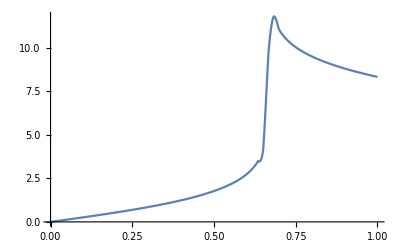

```mathematica
ahh=Interpolation[points];
Plot[ahh[x],{x,0,1}]
```